## Subroutines for quantum computing

```mathematica
Needs["QDENSITY`Qdensity`"]
```

Type "?intro", "?QDENSITY`Qdensity`*" or "?about for help.

```mathematica
?QDENSITY`Qdensity`*
```

## Impact of depolarization

```mathematica
w=.;
η=.;
E1=.;
ComplexExpand[Integrate[Exp[(I(w-E1)-η)t],{t,0,∞}]]
ComplexExpand[Integrate[I t Exp[(I(w-E1)-η)t],{t,0,∞}]]
```

ConditionalExpression[η/((E1-w)^2+η^2)+ⅈ (-E1/((E1-w)^2+η^2)+w/((E1-w)^2+η^2)),Im[w]+Re[η]>Im[E1]]

ConditionalExpression[(2 E1 η)/(((E1-w)^2+η^2)^2)-(2 w η)/(((E1-w)^2+η^2)^2)+ⅈ (-E1^2/(((E1-w)^2+η^2)^2)+(2 E1 w)/(((E1-w)^2+η^2)^2)-w^2/(((E1-w)^2+η^2)^2)+η^2/(((E1-w)^2+η^2)^2)),Im[w]+Re[η]>Im[E1]]

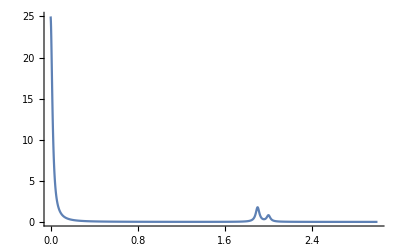

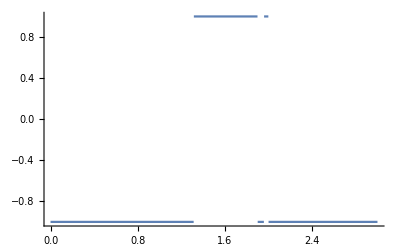

```mathematica
E1=1.9;
E2=2;
A1=0.07;
A2=0.03;
P=0.5;
η=0.02;
Plot[η/(w^2+η^2)P+(η/((E1-w)^2+η^2)A1+η/((E2-w)^2+η^2)A2)(1-P),{w,0,3},PlotRange->All]
Plot[Sign[-(2w η)/((w^2+η^2)^2)P+(-(2(w-E1) η)/(((E1-w)^2+η^2)^2)A1-(2(w-E2) η)/(((E2-w)^2+η^2)^2)A2)(1-P)],{w,0,3},PlotRange->All]
```

```mathematica
η0=.;
η1=.;
t=.;
M=({{1, I}, {-I, 0}});
Simplify[Norm[(Exp[-η0*t]-Exp[-η1*t])M]]
Norm[M]
```

Max[(√(ⅇ^(-2 t (η0+η1)) (-3 (ⅇ^(t (2 η0+η1))-ⅇ^(t (η0+2 η1))) Conjugate[ⅇ^(-t η0)-ⅇ^(-t η1)]-√5 √(ⅇ^(2 t (η0+η1)) (ⅇ^(t η0)-ⅇ^(t η1))^2 Conjugate[ⅇ^(-t η0)-ⅇ^(-t η1)]^2))))/(√2),(√(ⅇ^(-2 t (η0+η1)) (-3 (ⅇ^(t (2 η0+η1))-ⅇ^(t (η0+2 η1))) Conjugate[ⅇ^(-t η0)-ⅇ^(-t η1)]+√5 √(ⅇ^(2 t (η0+η1)) (ⅇ^(t η0)-ⅇ^(t η1))^2 Conjugate[ⅇ^(-t η0)-ⅇ^(-t η1)]^2))))/(√2)]

√(1/2 (3+√5))

```mathematica
FullSimplify[ⅇ^(-2 t (η0+η1)) (-3 (ⅇ^(t (2 η0+η1))-ⅇ^(t (η0+2 η1))) (ⅇ^(-t η0)-ⅇ^(-t η1))+√5 √(ⅇ^(2 t (η0+η1)) (ⅇ^(t η0)-ⅇ^(t η1))^2 (ⅇ^(-t η0)-ⅇ^(-t η1))^2))]
```

ⅇ^(-2 t (η0+η1)) (3 (ⅇ^(t η0)-ⅇ^(t η1))^2+√5 √((ⅇ^(t η0)-ⅇ^(t η1))^4))

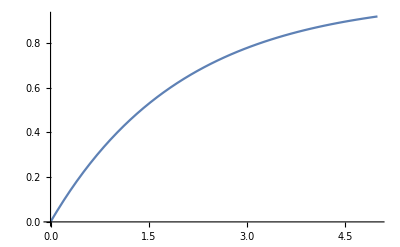

```mathematica
Plot[1-Exp[-0.5x],{x,0,5}]
```

```mathematica
Integrate[(1-u)^p,{u,0,1}]
```

ConditionalExpression[1/(1+p),Re[p]>-1]

```mathematica
Integrate[(1-u)^p Exp[-a u],{u,0,1}]
```

ConditionalExpression[(-a)^(-1-p) ⅇ^-a (Gamma[1+p]-Gamma[1+p,-a]),Re[p]>-1]

```mathematica
Integrate[(1-u)(1+Exp[-a u]),{u,0,1}]
```

(-2+2 a+a^2+2 ⅇ^-a)/(2 a^2)

```mathematica
Integrate[(1-u)Exp[-a u],{u,0,1}]
```

(-1+a+ⅇ^-a)/a^2

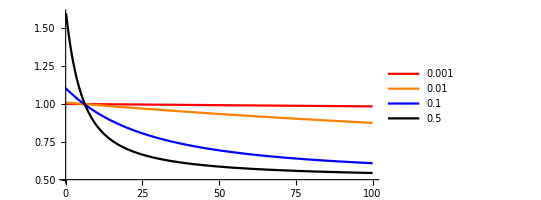

```mathematica
F[η_]:=1/2+(1+η)^2 Sum[(-η t)^n/((n+2)!),{n,0,∞}];
Plot[{F[0.001],F[0.01],F[0.1],F[0.5]},{t,0,100},PlotRange->{0.5,1.6},PlotStyle->{Red,Orange,Blue,Black},PlotLegends->Placed[{0.001,0.01,0.1,0.5},{0.85,0.75}],AspectRatio->0.5]
```

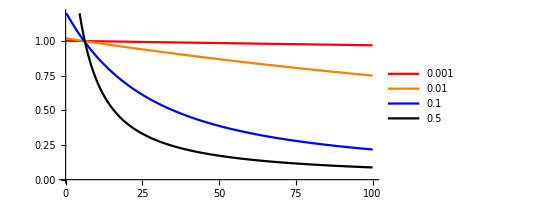

```mathematica
F[η_]:=2(1+η)^2 Sum[(-η t)^n/((n+2)!),{n,0,∞}];
Plot[{F[0.001],F[0.01],F[0.1],F[0.5]},{t,0,100},PlotRange->{0,1.2},PlotStyle->{Red,Orange,Blue,Black},PlotLegends->Placed[{0.001,0.01,0.1,0.5},{0.9,0.5}],AspectRatio->0.5]
```

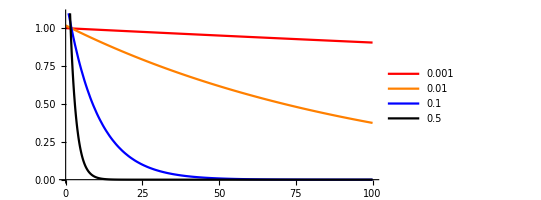

```mathematica
F[η_]:=(1+η)^2 Exp[-η t];
Plot[{F[0.001],F[0.01],F[0.1],F[0.5]},{t,0,100},PlotRange->{0,1.1},PlotStyle->{Red,Orange,Blue,Black},PlotLegends->Placed[{0.001,0.01,0.1,0.5},{0.85,0.75}],AspectRatio->0.5]
```